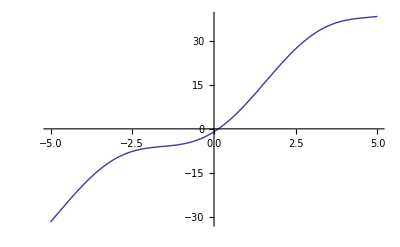

```mathematica
(*Зададим левую часть уравнения*)
f[x_]=7*x-6*Cos[x]+5;
(*Построим график данной функции*)
Plot[f[x],{x,-5,5}]
```

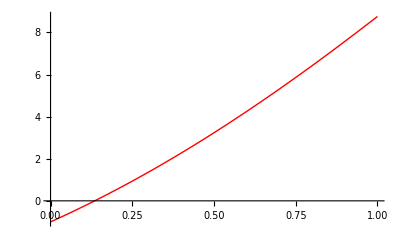

```mathematica
(*Локализуем корень уравнения*)
a=0;
b=1;
G=Plot[f[x],{x,a,b},PlotStyle->Red]
```

```mathematica
(*Метод половинного деления*)
(*Зададим точность вычислений*)
ϵ=10^(-3);
(*Зададим отрезок локализации корня*)
ad=a;
bd=b;
(*Найдем количество шагов метода половинного деления, используя априорную оценку*)
n=Floor[Log[2,(bd-ad)/ϵ]];
(*Зададим переменную для хранения приближений к корню*)
ID={};
(*Реализуем алгоритм метода половинного деления*)
For[k=1,k≤n,k++,
c=(ad+bd)/2;
AppendTo[ID,{c,0}];
If[f[c]==0,Break[]];
If[f[ad]*f[c]<0,
bd=c,
ad=c
]
];
Print["Корень уравнения равен: ",N[c]]
Print["Количество шагов метода равно: ",n]
(*Выполним анимацию приближения к корню уравнения*)
Animate[Show[G,ListPlot[{ID[[k]]}]],{k,1,n,1},AnimationRunning->False]
```

Корень уравнения равен: 0.134766

Количество шагов метода равно: 9

```mathematica
(*Метод хорд*)
(*Зададим точность вычислений*)
ϵ=10^(-3);
(*Зададим отрезок локализации корня*)
ac=a;
bc=b;
(*Найдем абсциссу точки пересечения хорды о осью абсцисс*)
c=(ac*f[bc]-bc*f[ac])/(f[bc]-f[ac]);
(*Зададим переменную для подсчета количества приближений к корню уравнения*)
n=1;
(*Зададим переменную для хранения приближений к корню*)
IC={{c,0}};
(*Зададим переменную для хранения построенных хорд*)
Lines={(f[bc]-f[ac])*(x-ac)/(bc-ac)+f[ac]};
(*Реализуем алгорит метода хорд*)
While[Abs[f[c]]≥ϵ,
If[f[c]==0,Break[]];
If[f[ac]*f[c]<0,
bc=c,
ac=c ];
c=(ac*f[bc]-bc*f[ac])/(f[bc]-f[ac]);
AppendTo[IC,{c,0}];
AppendTo[Lines,(f[bc]-f[ac])*(x-ac)/(bc-ac)+f[ac]];
n=n+1
];
Print["Корень уравнения равен: ",N[c]]
Print["Количество шагов метода равно: ",n]
Animate[Show[G,Plot[Lines[[k]],{x,a,b}],ListPlot[{IC[[k]]}]],{k,1,n,1},AnimationRunning->False]
```

Корень уравнения равен: 0.134961

Количество шагов метода равно: 5

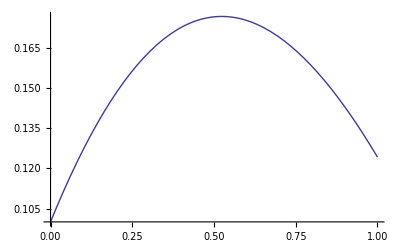

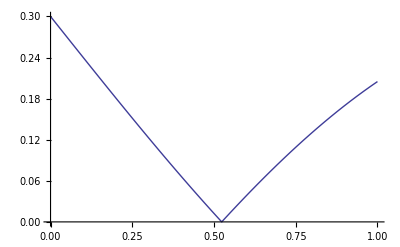

```mathematica
(*Метод итераций*)
(*Зададим отрезок локализации корня*)
ai=a;
bi=b;
(*Зададим параметр t*)
t=1/10;
(*Перейдем от исходного уравнения к равносильному уравнению вида x=g[x]*)
g[x_]=x-t*f[x];
(*Найдем производную функции g[x]*)
g1[x_]=D[g[x],x];
(*Построим график функции g[x] на отрезке [a;b]*)
Plot[g[x],{x,ai,bi}]
(*Построим график модуля производной функции g[x] на отрезке [a;b]*)
Plot[Abs[g1[x]],{x,a,b}]
```

```mathematica
(*Зададим константу сжатия*)
α=Abs[g1[ai]];
(*Зададим точность вычислений*)
ϵ=10^(-3);
(*Зададим начальное приближение*)
x0=ai;
(*Найдем первую итерацию*)
x1=g[ai];
(*Найдем количество итераций, используя априорную оценку теоремы Банаха*)
n=Floor[Log[α,ϵ*(1-α)/Abs[x1-x0]]]+1;
II={{x0,0},{x1,0}};
(*Реализуем алгоритм метода итераций*)
For[k=2,k≤n,k++,
x0=x1;
x1=g[x0];
AppendTo[II,{x1,0}]
];
Print["Корень уравнения равен: ",N[x1]]
Print["Количество итераций равно: ",n]
Animate[Show[G,ListPlot[{II[[k]]}]],{k,1,n,1},AnimationRunning->False]
```

Корень уравнения равен: 0.134966

Количество итераций равно: 5